# Pseudopotential method

by Aaron Danner.  E-mail the author with any questions or comments.  (Contact information is provided at http://www.ece.nus.edu.sg/stfpage/eleadj/index.htm.)

This program follows very closely the text at http://www.ece.nus.edu.sg/stfpage/eleadj/pseudopotential.htm although the text is not necessary to use the program.  This was created with Mathematica 5.2. The variable names should be consistent with the text description.  Cells in Mathematica are defined by the little blue bars on the right.  The black text below is in the first cell.  Put your cursor in there somewhere and use Shift+Enter to execute the code in a cell.  Then, execute subsequent cells.  Sometimes they may take awhile to execute.  You can see this when the blue bars on the right change to black during execution.  The variables which should be changed depending on the material of the band calculation are given in red.  Change the pseudopotentials until a few bandgaps in major crystal directions are consistent with measured values.  At that point then the rest of the bands should be accurate.  (* Comments appear in these enclosures *)

```mathematica
(* Set the size of the matrix to solve at each k point.  The matrix size is given by n, but set indirectly by using lim. *)
(* lim of 5 yields a 124x124 matrix with good accuracy.  lower is faster. *)
lim=5;
Clear[h,k,l,m,veck,Vs,Va,a,A]
(* Define basis reciprocal lattice vectors *)
vecb1={-1,1,1};
vecb2={1,-1,1};
vecb3={1,1,-1};
(* Offset because each cell has 2 atoms.  Use a symmetrical offset *)
vecT={1/8,1/8,1/8};
n=lim^3-1;
(* Functions used to help build matrix of reciprocal lattice vectors *)
h[m_]:=Floor[(m+n/2)/lim^2]-Floor[lim/2];
k[m_]:=Floor[Mod[m+n/2,lim^2]/lim]-Floor[lim/2];
l[m_]:=Mod[m+n/2,lim]-Floor[lim/2];
K[m_]:=h[m]*vecb1+k[m]*vecb2+l[m]*vecb3;
```

How do the functions for h, k, and l work?
The logic of the definitions of h, k, and l is as follows.  As m increments, we must cover all of the possible combinations of {h,k,l}.  Therefore, if lim=3, then as m is incremented {h,k,l} should cover all values between {-1,-1,-1} to {1,1,1}.  A value of lim=3 means that h can take on 3 values, in this case -1, 0, and 1.  If lim=5, then {h,k,l} must cover all integers in the range {-2,-2,-2} to {2,2,2}.  This takes place as follows in this example:

m	h	k	l
-2	0	0	-2
-1	0	0	-1
0	0	0	0
1	0	0	1
2	0	0	2
3	0	1	-2
4	0	1	-1
5	0	1	0
6	0	1	1
7	0	1	2
8	0	2	-2
etc.

```mathematica
(* Material parameters *)
a=5.6533; (* lattice constant in Angstroms *)
m0=9.11*10^-31; (* electron mass in kg *)
hbarJs=1.054*10^-34; (* hbar in J-s *)
hbareV=6.581*10^-16; (* hbar in eV-s *)

(* Pseudopotentials in eV (from Rydberg units, as is usual in publications) -- Change the first number in each definition. *)
(* The last number in each definition below identifies which form factor it is *)
Vs[m_]:=0
Vs[m_]:=-0.23*13.6059/;K[m].K[m]==3
Vs[m_]:=0*13.6059/;K[m].K[m]==4
Vs[m_]:=0.01*13.6059/;K[m].K[m]==8
Vs[m_]:=0.06*13.6059/;K[m].K[m]==11
Va[m_]:=0.07*13.6059/;K[m].K[m]==3
Va[m_]:=0.05*13.6059/;K[m].K[m]==4
Va[m_]:=0*13.6059/;K[m].K[m]==8
Va[m_]:=0.01*13.6059/;K[m].K[m]==11
Va[m_]:=0
                                                         
(* Definition of the potential and matrix elements *)
V[m_]:=Vs[m]*Cos[2 π K[m].vecT]+ⅈ*Va[m]*Sin[2 π K[m].vecT];
A[i_,j_,veck_]:=(hbarJs*hbareV)/(2 m0)*Abs[(veck+K[i]).(veck+K[i])]*KroneckerDelta[i,j]*((2 π)/(a*10^-10))^2+V[i-j];
(* Output the matrix size n x n -- This is n *)
n
```

124

```mathematica
(* kgenerator generates k values for m = 0 to 40 to make a complete band diagram; m is the x axis of a band diagram *)
(* this is merely a function definition that is later used *)
kgenerator[m_]:={0.5-m/20,0.5-m/20,0.5-m/20}/;m≤10 (* L(.5,.5,.5) to Γ(0,0,0) 10 points *)
kgenerator[m_]:={(m-10)/10,0,0}/;m>10&&m≤20 (* Γ(0,0,0) to X(1,0,0) 10 points *)
kgenerator[m_]:={1,(m-20)/10,0}/;m>20&&m≤25 (* X(1,0,0) to W(1,.5,0) 5 points *)
kgenerator[m_]:={1-(m-25)/20,0.5+(m-25)/20,0}/;m>25&&m≤30 (* W(1,.5,0) to K(.75,.75,0) *)
kgenerator[m_]:={0.75-(m-30)/(40/3),0.75-(m-30)/(40/3),0} (* K to Γ *)
```

```mathematica
(* This solves the band diagram at three symmetry points.  The list of values represent energies in eV of bands crossing the given symmetry point.  They are not referenced to any energy.  Only their relationship to each other matters.  A full diagram calculation is in the next cell.  *)
(* Solve the Γ point *)
matrixA = Table[A[i,j,{0,0,0}],{i,-n/2,n/2},{j,-n/2,n/2}];
gammalist=Take[Re[Eigenvalues[matrixA]],-10]
(* X Point *)
matrixA = Table[A[i,j,{1,0,0}],{i,-n/2,n/2},{j,-n/2,n/2}];
xlist=Take[Re[Eigenvalues[matrixA]],-10]
(* L Point *)
matrixA = Table[A[i,j,{.5,.5,.5}],{i,-n/2,n/2},{j,-n/2,n/2}];
llllist=Take[Re[Eigenvalues[matrixA]],-10]
```

{17.4469,16.8254,13.2345,13.2197,13.2126,10.208,8.79742,8.78691,8.78268,-3.40858}

{21.3959,21.2743,20.9404,20.9229,10.8616,10.5558,6.55505,6.54398,2.70561,-1.34793}

{20.4751,20.3881,17.3924,13.7481,13.7427,10.4826,7.90002,7.8978,2.84166,-1.94689}

```mathematica
(* Output the entire band diagram and save to a file.  Enter the filename below.  You may have to search for it, since Mathematica puts files in weird places.  Open in Excel by importing as a comma separated text file.  Each row represents a vertical slice of a band diagram. Top rows are left slices.  The numbers are not referenced to any particular energy, although the unit is correct in eV.  Usually the values are shifted so that the highest valence band gets energy of zero.  This takes some time to execute *)
outputband=Table[
matrixA=Table[A[i,j,kgenerator[m]],{i,-n/2,n/2},{j,-n/2,n/2}];
locallist=Take[Re[Eigenvalues[matrixA]]-8.52357,-15];Print[locallist];locallist,{m,0,40}]
(* filename in quotes next line *)
Export["gaasband.out",outputband,"CSV"];
```

{20.4895,13.4746,13.4544,13.2468,11.961,11.9515,11.8645,8.8688,5.22457,5.21916,1.95901,-0.623551,-0.625769,-5.68191,-10.4705}

{18.7957,14.2246,14.1936,14.0833,11.297,11.294,11.0609,8.90377,5.24164,5.23672,1.97982,-0.611209,-0.613501,-5.56693,-10.531}

{17.219,15.3472,15.3124,15.239,10.44,10.4376,10.0266,8.98632,5.29814,5.29326,2.04885,-0.566096,-0.568564,-5.24611,-10.684}

{16.9261,16.564,16.5356,15.3198,9.65703,9.65451,9.436,8.7153,5.37638,5.37109,2.16335,-0.49003,-0.492747,-4.7572,-10.8935}

{18.2121,17.4103,17.3962,13.9867,9.61656,9.02021,9.0169,7.7852,5.44203,5.43589,2.31684,-0.38629,-0.389296,-4.13922,-11.1237}

{19.2311,16.4806,16.4775,12.7227,9.91084,8.59077,8.5862,6.83205,5.44328,5.43605,2.49438,-0.260282,-0.263592,-3.42415,-11.3476}

{18.1087,15.4367,15.4344,11.7895,10.0891,8.41233,8.40654,5.9527,5.33695,5.32891,2.65977,-0.120511,-0.124121,-2.6378,-11.5474}

{16.9398,14.5048,14.5029,11.6467,9.71761,8.46202,8.45542,5.23026,5.13886,5.13062,2.72359,0.0203208,0.0164344,-1.80442,-11.7115}

{15.8728,13.7387,13.7369,12.0879,9.03546,8.64721,8.64001,4.92075,4.91263,4.80808,2.52445,0.144719,0.140601,-0.955414,-11.8328}

{14.9655,13.2116,13.2096,12.6753,8.84513,8.83739,8.50196,4.75724,4.74917,4.70449,2.03859,0.231929,0.227652,-0.160968,-11.9071}

{14.5014,13.0385,13.018,13.0164,8.93134,8.92334,8.30183,4.7109,4.69617,4.68905,1.68444,0.273852,0.263339,0.259108,-11.9321}

{15.1433,13.1098,13.0914,12.8763,8.9767,8.66945,8.54356,4.86803,4.84859,4.52697,2.16903,0.172231,0.161279,-0.200224,-11.8988}

{16.5112,13.3349,13.3165,12.8421,9.2613,9.11261,7.97892,5.30496,5.28597,4.12684,3.00938,-0.0861324,-0.0974204,-0.999506,-11.7996}

{18.2068,13.7106,13.692,13.054,10.2056,9.33879,7.28355,5.93984,5.92126,3.88517,3.59287,-0.426115,-0.43771,-1.82856,-11.6369}

{20.1,14.2344,14.2154,13.47,11.3182,9.65439,6.97742,6.70595,6.68772,4.32873,3.16996,-0.784639,-0.796415,-2.63725,-11.4156}

{19.3782,14.8927,14.8734,14.0685,12.5506,10.058,7.56058,7.54269,7.42071,4.1695,2.77115,-1.12259,-1.13443,-3.40873,-11.1432}

{18.1006,15.6141,15.5942,14.8512,13.8575,10.5466,8.47816,8.46052,8.33275,3.68216,2.44826,-1.4173,-1.42911,-4.1284,-10.8327}

{17.1,15.8754,15.8537,15.8424,15.0942,11.114,9.44453,9.42708,9.41088,3.17576,2.214,-1.65558,-1.66728,-4.77458,-10.5056}

{16.8681,16.0395,15.3197,15.0016,14.9901,11.7433,10.5541,10.4518,10.4345,2.75403,2.07446,-1.82959,-1.84112,-5.31105,-10.1974}

{18.0321,15.1341,14.2713,13.8991,13.8809,12.3765,11.7285,11.4923,11.4749,2.45755,2.02644,-1.93473,-1.94605,-5.68129,-9.96384}

{19.0318,14.6493,13.137,12.9785,12.9363,12.8723,12.7508,12.4169,12.3994,2.33804,2.03224,-1.96852,-1.97959,-5.81796,-9.8715}

{18.6756,15.1594,14.4213,13.6785,12.9359,12.7989,12.5514,11.545,11.2293,2.54039,2.22176,-2.04155,-2.07342,-5.79835,-9.86779}

{18.0738,16.4202,16.0795,13.9557,12.9998,12.8307,12.5505,10.1573,9.7548,3.09933,2.74507,-2.2112,-2.31274,-5.74547,-9.8591}

{17.8148,17.5291,17.4302,14.1241,13.0863,12.868,12.5638,8.78762,8.34966,3.91238,3.51301,-2.39349,-2.58275,-5.67417,-9.84823}

{19.003,17.4134,17.1935,14.2567,13.1717,12.8996,12.5807,7.48353,7.05716,4.90143,4.43868,-2.52434,-2.78712,-5.60943,-9.83872}

{19.032,17.3021,17.0676,14.3207,13.2295,12.9174,12.5958,6.34508,6.14854,5.9583,5.2096,-2.56915,-2.86205,-5.57953,-9.83352}

{18.8444,17.4969,16.653,14.6545,13.8117,12.536,12.0474,6.66586,6.53559,5.80993,4.75268,-2.47177,-2.90177,-5.57814,-9.84307}

{19.0441,17.3911,16.3231,15.2071,14.5286,11.8977,11.3599,7.30957,7.06588,5.73939,3.9741,-2.23077,-2.98165,-5.58153,-9.86288}

{18.6706,17.1932,16.2962,15.671,15.2858,11.1718,10.6387,7.99762,7.69905,5.67434,3.29028,-1.94373,-3.05046,-5.58902,-9.88369}

{17.8647,17.0661,16.8164,16.1176,15.6804,10.443,9.91309,8.69364,8.37149,5.63087,2.81161,-1.70142,-3.09434,-5.59616,-9.89879}

{17.5672,17.1818,16.8754,16.832,15.6666,9.97172,9.30377,9.23713,8.87807,5.61589,2.63484,-1.60313,-3.10927,-5.59897,-9.90419}

{18.507,17.9798,17.8003,15.9759,14.791,9.17407,8.55093,8.37628,8.11247,6.91244,2.92397,-1.37016,-3.22809,-5.47293,-10.0116}

{18.9719,18.6759,17.0241,15.017,13.9318,9.33514,8.49458,7.61067,7.56566,6.82847,3.25179,-1.09833,-3.10742,-5.26692,-10.2008}

{19.5252,18.7376,15.2294,14.0664,13.1014,11.0713,7.96522,7.00199,6.93729,6.18111,3.57173,-0.806454,-2.79477,-4.93291,-10.463}

{20.1433,17.2381,14.1324,13.1339,12.7017,12.0914,7.61766,6.63413,6.35288,5.59276,3.79866,-0.517994,-2.34564,-4.44991,-10.7675}

{18.8425,16.0089,15.2798,12.4547,12.4159,10.7476,7.47769,6.51006,5.85414,5.12092,3.83209,-0.258127,-1.80776,-3.82232,-11.0779}

{17.734,17.1865,14.6188,12.0887,11.4383,9.50018,7.55627,6.47609,5.44155,4.78522,3.65521,-0.0476973,-1.22742,-3.06571,-11.3639}

{17.8948,15.6676,13.8626,11.9766,10.3751,8.83915,7.83874,6.12669,5.11729,4.59821,3.32565,0.103463,-0.660056,-2.2005,-11.6039}

{16.4166,14.3633,13.3794,12.1569,9.37248,8.77675,8.2691,5.43446,4.8838,4.56428,2.84354,0.198463,-0.175842,-1.25682,-11.7837}

{15.1619,13.399,13.1131,12.6258,8.89052,8.71538,8.59371,4.88507,4.74289,4.64216,2.17704,0.248243,0.150397,-0.307418,-11.8947}

{14.5014,13.0385,13.018,13.0164,8.93134,8.92334,8.30183,4.7109,4.69617,4.68905,1.68444,0.273852,0.263339,0.259108,-11.9321}

{{20.4895,13.4746,13.4544,13.2468,11.961,11.9515,11.8645,8.8688,5.22457,5.21916,1.95901,-0.623551,-0.625769,-5.68191,-10.4705},{18.7957,14.2246,14.1936,14.0833,11.297,11.294,11.0609,8.90377,5.24164,5.23672,1.97982,-0.611209,-0.613501,-5.56693,-10.531},{17.219,15.3472,15.3124,15.239,10.44,10.4376,10.0266,8.98632,5.29814,5.29326,2.04885,-0.566096,-0.568564,-5.24611,-10.684},{16.9261,16.564,16.5356,15.3198,9.65703,9.65451,9.436,8.7153,5.37638,5.37109,2.16335,-0.49003,-0.492747,-4.7572,-10.8935},{18.2121,17.4103,17.3962,13.9867,9.61656,9.02021,9.0169,7.7852,5.44203,5.43589,2.31684,-0.38629,-0.389296,-4.13922,-11.1237},{19.2311,16.4806,16.4775,12.7227,9.91084,8.59077,8.5862,6.83205,5.44328,5.43605,2.49438,-0.260282,-0.263592,-3.42415,-11.3476},{18.1087,15.4367,15.4344,11.7895,10.0891,8.41233,8.40654,5.9527,5.33695,5.32891,2.65977,-0.120511,-0.124121,-2.6378,-11.5474},{16.9398,14.5048,14.5029,11.6467,9.71761,8.46202,8.45542,5.23026,5.13886,5.13062,2.72359,0.0203208,0.0164344,-1.80442,-11.7115},{15.8728,13.7387,13.7369,12.0879,9.03546,8.64721,8.64001,4.92075,4.91263,4.80808,2.52445,0.144719,0.140601,-0.955414,-11.8328},{14.9655,13.2116,13.2096,12.6753,8.84513,8.83739,8.50196,4.75724,4.74917,4.70449,2.03859,0.231929,0.227652,-0.160968,-11.9071},{14.5014,13.0385,13.018,13.0164,8.93134,8.92334,8.30183,4.7109,4.69617,4.68905,1.68444,0.273852,0.263339,0.259108,-11.9321},{15.1433,13.1098,13.0914,12.8763,8.9767,8.66945,8.54356,4.86803,4.84859,4.52697,2.16903,0.172231,0.161279,-0.200224,-11.8988},{16.5112,13.3349,13.3165,12.8421,9.2613,9.11261,7.97892,5.30496,5.28597,4.12684,3.00938,-0.0861324,-0.0974204,-0.999506,-11.7996},{18.2068,13.7106,13.692,13.054,10.2056,9.33879,7.28355,5.93984,5.92126,3.88517,3.59287,-0.426115,-0.43771,-1.82856,-11.6369},{20.1,14.2344,14.2154,13.47,11.3182,9.65439,6.97742,6.70595,6.68772,4.32873,3.16996,-0.784639,-0.796415,-2.63725,-11.4156},{19.3782,14.8927,14.8734,14.0685,12.5506,10.058,7.56058,7.54269,7.42071,4.1695,2.77115,-1.12259,-1.13443,-3.40873,-11.1432},{18.1006,15.6141,15.5942,14.8512,13.8575,10.5466,8.47816,8.46052,8.33275,3.68216,2.44826,-1.4173,-1.42911,-4.1284,-10.8327},{17.1,15.8754,15.8537,15.8424,15.0942,11.114,9.44453,9.42708,9.41088,3.17576,2.214,-1.65558,-1.66728,-4.77458,-10.5056},{16.8681,16.0395,15.3197,15.0016,14.9901,11.7433,10.5541,10.4518,10.4345,2.75403,2.07446,-1.82959,-1.84112,-5.31105,-10.1974},{18.0321,15.1341,14.2713,13.8991,13.8809,12.3765,11.7285,11.4923,11.4749,2.45755,2.02644,-1.93473,-1.94605,-5.68129,-9.96384},{19.0318,14.6493,13.137,12.9785,12.9363,12.8723,12.7508,12.4169,12.3994,2.33804,2.03224,-1.96852,-1.97959,-5.81796,-9.8715},{18.6756,15.1594,14.4213,13.6785,12.9359,12.7989,12.5514,11.545,11.2293,2.54039,2.22176,-2.04155,-2.07342,-5.79835,-9.86779},{18.0738,16.4202,16.0795,13.9557,12.9998,12.8307,12.5505,10.1573,9.7548,3.09933,2.74507,-2.2112,-2.31274,-5.74547,-9.8591},{17.8148,17.5291,17.4302,14.1241,13.0863,12.868,12.5638,8.78762,8.34966,3.91238,3.51301,-2.39349,-2.58275,-5.67417,-9.84823},{19.003,17.4134,17.1935,14.2567,13.1717,12.8996,12.5807,7.48353,7.05716,4.90143,4.43868,-2.52434,-2.78712,-5.60943,-9.83872},{19.032,17.3021,17.0676,14.3207,13.2295,12.9174,12.5958,6.34508,6.14854,5.9583,5.2096,-2.56915,-2.86205,-5.57953,-9.83352},{18.8444,17.4969,16.653,14.6545,13.8117,12.536,12.0474,6.66586,6.53559,5.80993,4.75268,-2.47177,-2.90177,-5.57814,-9.84307},{19.0441,17.3911,16.3231,15.2071,14.5286,11.8977,11.3599,7.30957,7.06588,5.73939,3.9741,-2.23077,-2.98165,-5.58153,-9.86288},{18.6706,17.1932,16.2962,15.671,15.2858,11.1718,10.6387,7.99762,7.69905,5.67434,3.29028,-1.94373,-3.05046,-5.58902,-9.88369},{17.8647,17.0661,16.8164,16.1176,15.6804,10.443,9.91309,8.69364,8.37149,5.63087,2.81161,-1.70142,-3.09434,-5.59616,-9.89879},{17.5672,17.1818,16.8754,16.832,15.6666,9.97172,9.30377,9.23713,8.87807,5.61589,2.63484,-1.60313,-3.10927,-5.59897,-9.90419},{18.507,17.9798,17.8003,15.9759,14.791,9.17407,8.55093,8.37628,8.11247,6.91244,2.92397,-1.37016,-3.22809,-5.47293,-10.0116},{18.9719,18.6759,17.0241,15.017,13.9318,9.33514,8.49458,7.61067,7.56566,6.82847,3.25179,-1.09833,-3.10742,-5.26692,-10.2008},{19.5252,18.7376,15.2294,14.0664,13.1014,11.0713,7.96522,7.00199,6.93729,6.18111,3.57173,-0.806454,-2.79477,-4.93291,-10.463},{20.1433,17.2381,14.1324,13.1339,12.7017,12.0914,7.61766,6.63413,6.35288,5.59276,3.79866,-0.517994,-2.34564,-4.44991,-10.7675},{18.8425,16.0089,15.2798,12.4547,12.4159,10.7476,7.47769,6.51006,5.85414,5.12092,3.83209,-0.258127,-1.80776,-3.82232,-11.0779},{17.734,17.1865,14.6188,12.0887,11.4383,9.50018,7.55627,6.47609,5.44155,4.78522,3.65521,-0.0476973,-1.22742,-3.06571,-11.3639},{17.8948,15.6676,13.8626,11.9766,10.3751,8.83915,7.83874,6.12669,5.11729,4.59821,3.32565,0.103463,-0.660056,-2.2005,-11.6039},{16.4166,14.3633,13.3794,12.1569,9.37248,8.77675,8.2691,5.43446,4.8838,4.56428,2.84354,0.198463,-0.175842,-1.25682,-11.7837},{15.1619,13.399,13.1131,12.6258,8.89052,8.71538,8.59371,4.88507,4.74289,4.64216,2.17704,0.248243,0.150397,-0.307418,-11.8947},{14.5014,13.0385,13.018,13.0164,8.93134,8.92334,8.30183,4.7109,4.69617,4.68905,1.68444,0.273852,0.263339,0.259108,-11.9321}}

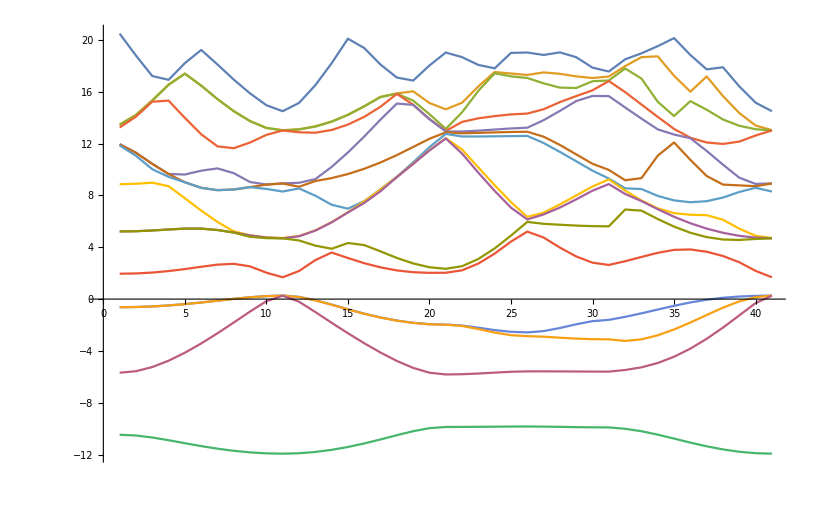

```mathematica
ListPlot[Transpose[%40], Joined->True]
```